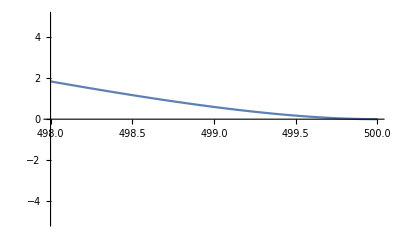

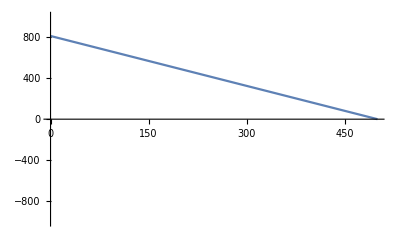

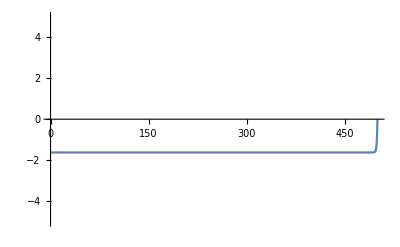

((-1/ⅇ^500+1/ⅇ^200+ⅇ^200-ⅇ^500) Tan[45])/(-1/ⅇ^500+ⅇ^500)

```mathematica
h[x_]:= ((Tan[45]*(E^x-E^500+E^(-x)-E^(-500)))/(E^(500-E^(-500))))+Tan[45]*(500-x)
g[x_]:= Tan[45]*(500-x)
f[x_]:=((Tan[45]*(Exp[x]-Exp[500]+Exp[-x]-Exp[-500]))/(Exp[500]-Exp[-500]))
Plot[h[x],{x, 498, 500}, PlotRange->5]
Plot[g[x],{x,0, 500}, PlotRange->1000]
Plot[f[x],{x, 0, 500}, PlotRange->5]
f[200]
```

```mathematica
N[((-1/ⅇ^500+1/ⅇ^200+ⅇ^200-ⅇ^500) Tan[45])/(-1/ⅇ^500+ⅇ^500)]
```

-1.61978